## Linear Single track model

```mathematica
Clear[SimpleNonlinearBicycleModel]
SimpleNonlinearBicycleModel[vx_ : 10,px0_:0,py0_:0] := 
 Module[{m = 1555, theta = 2491, lh = 1.372, lv = 1.354, cav = 100000,
    cah = 160000}, 
  NonlinearStateSpaceModel[{β'[
      t] == (-1 - (cav*lv - cah*lh)/(m vx^2)) ψ'[
        t] - (cav + cah)/(m vx) β[t] + 
      1/vx cav/m δ[t], ψ''[
      t] == -((cav*lv^2 + cah*lh^2)/( vx theta)) ψ'[
        t] - (cav*lv - cah*lh)/theta β[t] + (cav*lv)/
       theta δ[t],
    px'[t] == vx*Cos[ψ[t]] - vx*Sin[ψ[t]]*β[t], 
    py'[t] == 
     vx*Sin[ψ[t]] + vx*Cos[ψ[t]]*β[t] }, {β[
     t], ψ[t], ψ'[t], {px[t],px0}, {py[t],py0}}, {δ[t]}, {px[t], 
    py[t]}, t]]
```

## Reference trajectory

```mathematica
pos=Import[FileNameJoin[{NotebookDirectory[],"./position.csv"}]]ᵀ;
```

## Model discretization

```mathematica
dsys=ToDiscreteTimeModel[SimpleNonlinearBicycleModel[29,First[pos[[1]]],First[pos[[2]]]],0.1]
```

β[k]+0.1 (0.-5.76561 (0.+β[k]-0.384615 δ[k]+0.162286 x_1[k]))ψ[k]+0.1 (0.+1. x_1[k])0.1 (0.+1. (33.7696 β[k]+54.3557 δ[k]-6.70708 x_1[k]))+x_1[k]px[k]+0.1 (0.+1. (29 Cos[ψ[k]]-29 Sin[ψ[k]] β[k]))py[k]+0.1 (0.+1. (29 Sin[ψ[k]]+29 Cos[ψ[k]] β[k]))px[k]py[k]β[k]ψ[k]x_1[k]{px[k],4.4113}{py[k],-2.6729}0.15122NoneNoneFalseFalseFalse{δ[k]}k

## MPC setup

```mathematica
costTracker=<|"Norm"->2,"Horizon"->30,"ErrorWeight"-> DiagonalMatrix[{10,10}],"InputIncrementWeight"->DiagonalMatrix[{10}]|>
```

<|Norm→2,Horizon→30,ErrorWeight→{{10,0},{0,10}},InputIncrementWeight→{{10}}|>

```mathematica
mpc=ModelPredictiveController[dsys,costTracker,{}]
```

SystemsModelControllerData[<|TrackingMethod -> InputIncrement, Design -> MPC tracker, InputModel -> NonlinearStateSpaceModel[{{β[k] + 0.1 (0. - 5.76561 (0. + β[k] - 0.384615 δ[k] + 0.162286 x [k])), ψ[k] + 0.1 <<1>>, <<2>>, py[k] + 0.1 (0. + 1. (29 Sin[ψ[k]] + 29 Cos[ψ[k]] β[k]))}, {<<2>>}}, <<5>>], <<33>>, SummaryItemsFunction -> Control`MPCDump`mpcSummaryItems|>, {<<21>>}]
                                                                                                                                                                                               1

```mathematica
csys=mpc["ClosedLoopSystem"]
```

SystemsConnectionsModel[…]

## System simulation

```mathematica
res=OutputResponse[csys,#[[1;;60]]&/@ref];
```

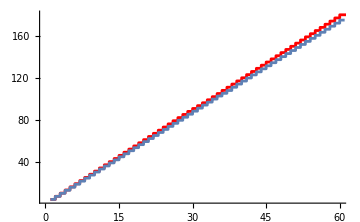
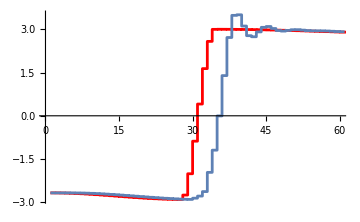

```mathematica
Table[l1=ListStepPlot[{ref[[p]]},PlotStyle->{Red,Dashed}];
l2=ListStepPlot[res[[p]]];
Show[l1,l2,PlotRange->{{0,60},Automatic},ImageSize->Medium],{p,{1,2}}]
```